# FlexEL

```mathematica
Clear["`*"];
```

## MATRIX P:

```mathematica
-Graphics-;
```

```mathematica
PP=({{1, -x, -y, -x^2/2, -x^3/6, -((x^2 y)/2+y^4/12), -(x^3 y)/6, -y^2/2, -((y^2 x)/2+x^4/12), -y^3/6, -(y^3 x)/6, -x y/2}, {0, 1, 0, x, x^2/2, x y, (x^2 y)/2, 0, y^2/2+x^3/3, 0, y^3/6, y/2}, {0, 0, 1, 0, 0, y^3/3+x^2/2, x^3/6, y, x y, y^2/2, (y^2 x)/2, x/2}});
```

## MATRIX C (combinations of P calculated on nodes):

```mathematica
-Graphics-;
```

```mathematica
x1=-1;y1=-1;x2=1;y2=-1;x3=1;y3=1;x4=-1;y4=1;
```

```mathematica
PP1=PP/.x->x1/.y->y1;
PP2=PP/.x->x2/.y->y2;
PP3=PP/.x->x3/.y->y3;
PP4=PP/.x->x4/.y->y4;
```

Unisco le matrici per costruire la matrice C

```mathematica
CC=Join[PP1,PP2,PP3,PP4];
```

```mathematica
NN=PP.Inverse[CC];
```

```mathematica
NN//MatrixForm
```

(1/4-(3 x)/8+x^3/8-(3 y)/8+(x y)/2-(x^3 y)/8+y^3/8-(x y^3)/8 | -7/48+x/8+x^2/8-x^3/8+y/8-(x y)/8+(x^3 y)/8+y^2/24+1/4 (-(x^2 y)/2-y^4/12) | -7/48+x/8+x^2/24+y/8-(x y)/8+y^2/8-y^3/8+(x y^3)/8+1/4 (-x^4/12-(x y^2)/2) | 1/4+(3 x)/8-x^3/8-(3 y)/8-(x y)/2+(x^3 y)/8+y^3/8+(x y^3)/8 | 7/48+x/8-x^2/8-x^3/8-y/8-(x y)/8+(x^3 y)/8-y^2/24+1/4 ((x^2 y)/2+y^4/12) | -5/48-x/8-x^2/24+y/8+(x y)/8+y^2/8-y^3/8-(x y^3)/8+1/4 (x^4/12+(x y^2)/2) | 1/4+(3 x)/8-x^3/8+(3 y)/8+(x y)/2-(x^3 y)/8-y^3/8-(x y^3)/8 | 5/48+x/8-x^2/8-x^3/8+y/8+(x y)/8-(x^3 y)/8+y^2/24+1/4 (-(x^2 y)/2-y^4/12) | 5/48+x/8+x^2/24+y/8+(x y)/8-y^2/8-y^3/8-(x y^3)/8+1/4 (-x^4/12-(x y^2)/2) | 1/4-(3 x)/8+x^3/8+(3 y)/8-(x y)/2+(x^3 y)/8-y^3/8+(x y^3)/8 | -5/48+x/8+x^2/8-x^3/8-y/8+(x y)/8-(x^3 y)/8-y^2/24+1/4 ((x^2 y)/2+y^4/12) | 7/48-x/8-x^2/24+y/8-(x y)/8-y^2/8-y^3/8+(x y^3)/8+1/4 (x^4/12+(x y^2)/2)
3/8-(3 x^2)/8-y/2+(3 x^2 y)/8+y^3/8 | -1/8-x/4+(3 x^2)/8+y/8+(x y)/4-(3 x^2 y)/8 | -1/8-x/12+y/8-y^3/8+1/4 (x^3/3+y^2/2) | -3/8+(3 x^2)/8+y/2-(3 x^2 y)/8-y^3/8 | -1/8+x/4+(3 x^2)/8+y/8-(x y)/4-(3 x^2 y)/8 | 1/8+x/12-y/8+y^3/8+1/4 (-x^3/3-y^2/2) | -3/8+(3 x^2)/8-y/2+(3 x^2 y)/8+y^3/8 | -1/8+x/4+(3 x^2)/8-y/8+(x y)/4+(3 x^2 y)/8 | -1/8-x/12-y/8+y^3/8+1/4 (x^3/3+y^2/2) | 3/8-(3 x^2)/8+y/2-(3 x^2 y)/8-y^3/8 | -1/8-x/4+(3 x^2)/8-y/8-(x y)/4+(3 x^2 y)/8 | 1/8+x/12+y/8-y^3/8+1/4 (-x^3/3-y^2/2)
3/8-x/2+x^3/8-(3 y^2)/8+(3 x y^2)/8 | -1/8+x/8-x^3/8-y/12+1/4 (x^2/2+y^3/3) | -1/8+x/8-y/4+(x y)/4+(3 y^2)/8-(3 x y^2)/8 | 3/8+x/2-x^3/8-(3 y^2)/8-(3 x y^2)/8 | 1/8+x/8-x^3/8+y/12+1/4 (-x^2/2-y^3/3) | -1/8-x/8-y/4-(x y)/4+(3 y^2)/8+(3 x y^2)/8 | -3/8-x/2+x^3/8+(3 y^2)/8+(3 x y^2)/8 | -1/8-x/8+x^3/8-y/12+1/4 (x^2/2+y^3/3) | -1/8-x/8+y/4+(x y)/4+(3 y^2)/8+(3 x y^2)/8 | -3/8+x/2-x^3/8+(3 y^2)/8-(3 x y^2)/8 | 1/8-x/8+x^3/8+y/12+1/4 (-x^2/2-y^3/3) | -1/8+x/8+y/4-(x y)/4+(3 y^2)/8-(3 x y^2)/8)

```mathematica
-Graphics-;
```

```mathematica
qe=({{W1}, {βx1}, {βy1}, {W2}, {βx2}, {βy2}, {W3}, {βx3}, {βy3}, {W4}, {βx4}, {βy4}});
```

```mathematica
-Graphics-;
```

```mathematica
U=({{W}, {βx}, {βy}});
```

```mathematica
W=NN[[1,1]]qe[[1,1]]+NN[[1,2]]qe[[2,1]]+NN[[1,3]]qe[[3,1]]+NN[[1,4]]qe[[4,1]]+NN[[1,5]]qe[[5,1]]+NN[[1,6]]qe[[6,1]]+NN[[1,7]]qe[[7,1]]+NN[[1,8]]qe[[8,1]]+NN[[1,9]]qe[[9,1]]+NN[[1,10]]qe[[10,1]]+NN[[1,11]]qe[[11,1]]+NN[[1,12]]qe[[12,1]];
βx=NN[[2,1]]qe[[1,1]]+NN[[2,2]]qe[[2,1]]+NN[[2,3]]qe[[3,1]]+NN[[2,4]]qe[[4,1]]+NN[[2,5]]qe[[5,1]]+NN[[2,6]]qe[[6,1]]+NN[[2,7]]qe[[7,1]]+NN[[2,8]]qe[[8,1]]+NN[[2,9]]qe[[9,1]]+NN[[2,10]]qe[[10,1]]+NN[[2,11]]qe[[11,1]]+NN[[2,12]]qe[[12,1]];
βy=NN[[3,1]]qe[[1,1]]+NN[[3,2]]qe[[2,1]]+NN[[3,3]]qe[[3,1]]+NN[[3,4]]qe[[4,1]]+NN[[3,5]]qe[[5,1]]+NN[[3,6]]qe[[6,1]]+NN[[3,7]]qe[[7,1]]+NN[[3,8]]qe[[8,1]]+NN[[3,9]]qe[[9,1]]+NN[[3,10]]qe[[10,1]]+NN[[3,11]]qe[[11,1]]+NN[[3,12]]qe[[12,1]];
```

```mathematica
Plot3D[NN[[1,12]],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

## Esempio:

```mathematica
-Graphics-;
```

Creo due elementi con spostamenti e rotazioni note e vedo se sono compatibili.

ELEMENTO 1:

```mathematica
q1=({{0}, {0}, {0}, {-1}, {2}, {3}, {-2}, {4}, {5}, {0}, {0}, {0}});
```

```mathematica
Wel1=W/.qe[[1,1]]->q1[[1,1]]/.qe[[2,1]]->q1[[2,1]]/.qe[[3,1]]->q1[[3,1]]/.qe[[4,1]]->q1[[4,1]]/.qe[[5,1]]->q1[[5,1]]/.qe[[6,1]]->q1[[6,1]]/.qe[[7,1]]->q1[[7,1]]/.qe[[8,1]]->q1[[8,1]]/.qe[[9,1]]->q1[[9,1]]/.qe[[10,1]]->q1[[10,1]]/.qe[[11,1]]->q1[[11,1]]/.qe[[12,1]]->q1[[12,1]];
```

```mathematica
βxel1=βx/.qe[[1,1]]->q1[[1,1]]/.qe[[2,1]]->q1[[2,1]]/.qe[[3,1]]->q1[[3,1]]/.qe[[4,1]]->q1[[4,1]]/.qe[[5,1]]->q1[[5,1]]/.qe[[6,1]]->q1[[6,1]]/.qe[[7,1]]->q1[[7,1]]/.qe[[8,1]]->q1[[8,1]]/.qe[[9,1]]->q1[[9,1]]/.qe[[10,1]]->q1[[10,1]]/.qe[[11,1]]->q1[[11,1]]/.qe[[12,1]]->q1[[12,1]];
```

```mathematica
βyel1=βy/.qe[[1,1]]->q1[[1,1]]/.qe[[2,1]]->q1[[2,1]]/.qe[[3,1]]->q1[[3,1]]/.qe[[4,1]]->q1[[4,1]]/.qe[[5,1]]->q1[[5,1]]/.qe[[6,1]]->q1[[6,1]]/.qe[[7,1]]->q1[[7,1]]/.qe[[8,1]]->q1[[8,1]]/.qe[[9,1]]->q1[[9,1]]/.qe[[10,1]]->q1[[10,1]]/.qe[[11,1]]->q1[[11,1]]/.qe[[12,1]]->q1[[12,1]];
```

Elemento 2:

```mathematica
q2=({{-1}, {2}, {3}, {0}, {0}, {0}, {0}, {0}, {0}, {-2}, {4}, {5}});
```

```mathematica
Wel2=W/.qe[[1,1]]->q2[[1,1]]/.qe[[2,1]]->q2[[2,1]]/.qe[[3,1]]->q2[[3,1]]/.qe[[4,1]]->q2[[4,1]]/.qe[[5,1]]->q2[[5,1]]/.qe[[6,1]]->q2[[6,1]]/.qe[[7,1]]->q2[[7,1]]/.qe[[8,1]]->q2[[8,1]]/.qe[[9,1]]->q2[[9,1]]/.qe[[10,1]]->q2[[10,1]]/.qe[[11,1]]->q2[[11,1]]/.qe[[12,1]]->q2[[12,1]];
```

```mathematica
βxel2=βx/.qe[[1,1]]->q2[[1,1]]/.qe[[2,1]]->q2[[2,1]]/.qe[[3,1]]->q2[[3,1]]/.qe[[4,1]]->q2[[4,1]]/.qe[[5,1]]->q2[[5,1]]/.qe[[6,1]]->q2[[6,1]]/.qe[[7,1]]->q2[[7,1]]/.qe[[8,1]]->q2[[8,1]]/.qe[[9,1]]->q2[[9,1]]/.qe[[10,1]]->q2[[10,1]]/.qe[[11,1]]->q2[[11,1]]/.qe[[12,1]]->q2[[12,1]];
```

```mathematica
βyel2=βy/.qe[[1,1]]->q2[[1,1]]/.qe[[2,1]]->q2[[2,1]]/.qe[[3,1]]->q2[[3,1]]/.qe[[4,1]]->q2[[4,1]]/.qe[[5,1]]->q2[[5,1]]/.qe[[6,1]]->q2[[6,1]]/.qe[[7,1]]->q2[[7,1]]/.qe[[8,1]]->q2[[8,1]]/.qe[[9,1]]->q2[[9,1]]/.qe[[10,1]]->q2[[10,1]]/.qe[[11,1]]->q2[[11,1]]/.qe[[12,1]]->q2[[12,1]];
```

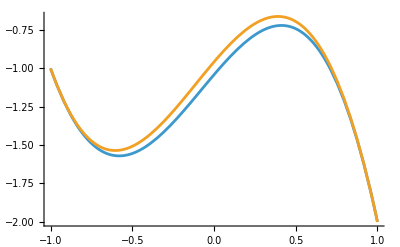

```mathematica
Plot[{Wel1/.x->1,Wel2/.x->-1},{y,-1,1}]
```

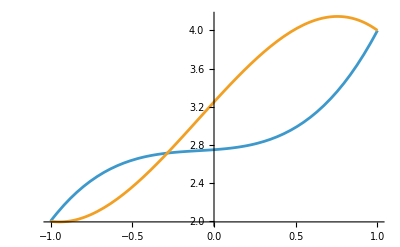

```mathematica
Plot[{βxel1/.x->1,βxel2/.x->-1},{y,-1,1}]
```

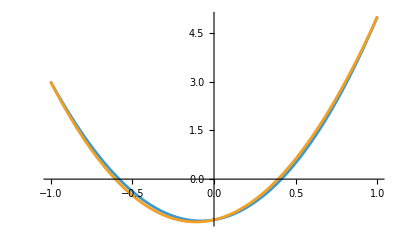

```mathematica
Plot[{βyel1/.x->1,βyel2/.x->-1},{y,-1,1}]
```

L’elemento NON è compatibile anche se sembra quasi per lo spostamento e la rotazione in y (vedi grafici dopo)

## Plotting Complicato:

Definisco la geometria indeformata (Posso usare le funzioni di forma del QL1 per x e y mentre userò W per z

```mathematica
xx1=5;
yy1=-5;
zz1=5;
n1={xx1,yy1,zz1};
```

```mathematica
xx2=10;
yy2=-5;
zz2=5;
n2={xx2,yy2,zz2};
```

```mathematica
xx3=11;
yy3=5;
zz3=6;
n3={xx3,yy3,zz3};
```

```mathematica
xx4=6;
yy4=5;
zz4=5;
n4={xx4,yy4,zz4};
```

```mathematica
xx5=13;
yy5=-5;
zz5=6;
n5={xx5,yy5,zz5};
```

```mathematica
xx6=14;
yy6=5;
zz6=8;
n6={xx6,yy6,zz6};
```

```mathematica
N1=1/4-y/4-x/4+(y x)/4;
N2=1/4-y/4+x/4-(y x)/4;
N3=1/4+y/4+x/4+(y x)/4;
N4=1/4+y/4-x/4-(y x)/4;
```

```mathematica
el1indef=N1 n1+N2 n2+N3 n3+N4 n4;
el2indef=N1 n2+N2 n5+N3 n6+N4 n3;
```

```mathematica
Pnode=ListPointPlot3D[{n1,n2,n3,n4,n5,n6},PlotStyle->Black];
```

```mathematica
P1=ParametricPlot3D[{el1indef,el2indef},{x,-1,1},{y,-1,1},PlotRange->All];
```

```mathematica
Pindef=Show[P1,Pnode,PlotRange->All]
```

-Graphics3D-

```mathematica
el1def={el1indef[[1]],el1indef[[2]],el1indef[[3]]+Wel1};
el2def={el2indef[[1]],el2indef[[2]],el2indef[[3]]+Wel2};
```

```mathematica
n1def={xx1,yy1,zz1+Wel1/.x->-1/.y->-1};
n2def={xx2,yy2,zz2+Wel1/.x->1/.y->-1};
n3def={xx3,yy3,zz3+Wel1/.x->1/.y->1};
n4def={xx4,yy4,zz4+Wel1/.x->-1/.y->1};
n5def={xx5,yy5,zz5+Wel2/.x->1/.y->-1};
n6def={xx6,yy6,zz6+Wel2/.x->1/.y->1};
```

```mathematica
Pnodedef=ListPointPlot3D[{n1def,n2def,n3def,n4def,n5def,n6def},PlotStyle->Black];
```

```mathematica
P2=ParametricPlot3D[{el1def,el2def},{x,-1,1},{y,-1,1},PlotRange->All];
```

```mathematica
Pdef=Show[P2,Pnodedef,PlotRange->All]
```

-Graphics3D-

## Calcolo delle tensioni:

Matrice Q

```mathematica
-Graphics-;
```

```mathematica
QQ=({{0, 0, 0, 1, x, y, x y, 0, x^2, 0, 0, 0}, {0, 0, 0, 0, 0, y^2, 0, 1, x, y, x y, 0}, {0, 0, 0, 0, 0, 2x, x^2, 0, 2y, 0, y^2, 1}});
```

```mathematica
DD=1/12({{(Em h^3)/(1-ν^2), ν (Em h^3)/(1-ν^2), 0}, {ν (Em h^3)/(1-ν^2), (Em h^3)/(1-ν^2), 0}, {0, 0, (Em h^3)/(1-ν^2) (1-ν)/2}});
Em=1;
ν=0.3;
h=1;
```

```mathematica
-Graphics-;
```

Elemento 1:

```mathematica
ϵ1=QQ.Inverse[CC].q1;
```

```mathematica
σ1=DD.ϵ1;
```

Elemento 2:

```mathematica
ϵ2=QQ.Inverse[CC].q2;
```

```mathematica
σ2=DD.ϵ2;
```

## Tensioni sul lato comune

σx:

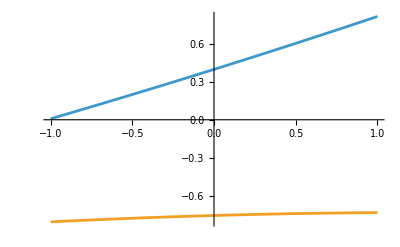

```mathematica
Plot[{σ1[[1,1]]/.x->1,σ2[[1,1]]/.x->-1},{y,-1,1}]
```

σy:

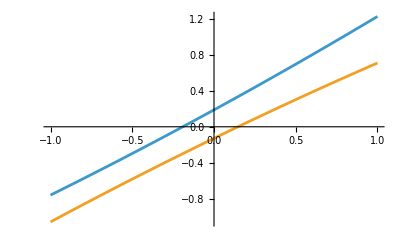

```mathematica
Plot[{σ1[[2,1]]/.x->1,σ2[[2,1]]/.x->-1},{y,-1,1}]
```

τxy:

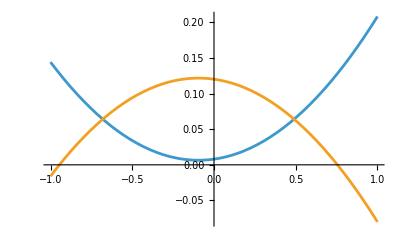

```mathematica
Plot[{σ1[[3,1]]/.x->1,σ2[[3,1]]/.x->-1},{y,-1,1}]
```

## ParametricPlot 3D σx

```mathematica
σσ1[x_,y_]=σ1[[1,1]];
σσ2[x_,y_]=σ2[[1,1]];
```

```mathematica
minS1=NMinimize[{σσ1[x,y],0<=x<=1,0<=y<=1},{x,y}][[1]]//Chop
minS2=NMinimize[{σσ2[x,y],0<=x<=1,0<=y<=1},{x,y}][[1]]//Chop
```

0.131258

-0.103785

```mathematica
maxS1=NMaximize[{σσ1[x,y],0<=x<=1,0<=y<=1},{x,y}][[1]]//Chop
maxS2=NMaximize[{σσ2[x,y],0<=x<=1,0<=y<=1},{x,y}][[1]]//Chop
```

0.813492

0.601343

```mathematica
PS1=ParametricPlot3D[{el1indef},{x,-1,1},{y,-1,1},ColorFunction->Function[{x,y,z},ColorData["TemperatureMap"][Rescale[σσ1[x,y],{Min[minS1,minS2],Max[maxS1,maxS2]}]]],MeshFunctions->{Function[{x,y,z},σσ1[x,y]]},MeshStyle->Directive[Black,Thin],Mesh->10,(*numero linee di livello*)Lighting->"Neutral"];
PS2=ParametricPlot3D[{el2indef},{x,-1,1},{y,-1,1},ColorFunction->Function[{x,y,z},ColorData["TemperatureMap"][Rescale[σσ2[x,y],{Min[minS1,minS2],Max[maxS1,maxS2]}]]],MeshFunctions->{Function[{x,y,z},σσ1[x,y]]},MeshStyle->Directive[Black,Thin],Mesh->10,(*numero linee di livello*)Lighting->"Neutral"];
```

```mathematica
Show[PS1,PS2,PlotRange->All]
```

-Graphics3D-

## ParametricPlot 3D σy

```mathematica
σσ1[x_,y_]=σ1[[2,1]];
σσ2[x_,y_]=σ2[[2,1]];
```

```mathematica
minS1=NMinimize[{σσ1[x,y],0<=x<=1,0<=y<=1},{x,y}][[1]]//Chop
minS2=NMinimize[{σσ2[x,y],0<=x<=1,0<=y<=1},{x,y}][[1]]//Chop
```

0.0671551

0.02442

```mathematica
maxS1=NMaximize[{σσ1[x,y],0<=x<=1,0<=y<=1},{x,y}][[1]]//Chop
maxS2=NMaximize[{σσ2[x,y],0<=x<=1,0<=y<=1},{x,y}][[1]]//Chop
```

1.23016

0.445665

```mathematica
PS1=ParametricPlot3D[{el1indef},{x,-1,1},{y,-1,1},ColorFunction->Function[{x,y,z},ColorData["TemperatureMap"][Rescale[σσ1[x,y],{Min[minS1,minS2],Max[maxS1,maxS2]}]]],MeshFunctions->{Function[{x,y,z},σσ1[x,y]]},MeshStyle->Directive[Black,Thin],Mesh->10,(*numero linee di livello*)Lighting->"Neutral"];
PS2=ParametricPlot3D[{el2indef},{x,-1,1},{y,-1,1},ColorFunction->Function[{x,y,z},ColorData["TemperatureMap"][Rescale[σσ2[x,y],{Min[minS1,minS2],Max[maxS1,maxS2]}]]],MeshFunctions->{Function[{x,y,z},σσ1[x,y]]},MeshStyle->Directive[Black,Thin],Mesh->10,(*numero linee di livello*)Lighting->"Neutral"];
```

```mathematica
Show[PS1,PS2,PlotRange->All]
```

-Graphics3D-

## ParametricPlot 3D τxy

```mathematica
σσ1[x_,y_]=σ1[[3,1]];
σσ2[x_,y_]=σ2[[3,1]];
```

```mathematica
minS1=NMinimize[{σσ1[x,y],0<=x<=1,0<=y<=1},{x,y}][[1]]//Chop
minS2=NMinimize[{σσ2[x,y],0<=x<=1,0<=y<=1},{x,y}][[1]]//Chop
```

-0.0480769

-0.187856

```mathematica
maxS1=NMaximize[{σσ1[x,y],0<=x<=1,0<=y<=1},{x,y}][[1]]//Chop
maxS2=NMaximize[{σσ2[x,y],0<=x<=1,0<=y<=1},{x,y}][[1]]//Chop
```

0.208333

0.0560897

```mathematica
PS1=ParametricPlot3D[{el1indef},{x,-1,1},{y,-1,1},ColorFunction->Function[{x,y,z},ColorData["TemperatureMap"][Rescale[σσ1[x,y],{Min[minS1,minS2],Max[maxS1,maxS2]}]]],MeshFunctions->{Function[{x,y,z},σσ1[x,y]]},MeshStyle->Directive[Black,Thin],Mesh->10,(*numero linee di livello*)Lighting->"Neutral"];
PS2=ParametricPlot3D[{el2indef},{x,-1,1},{y,-1,1},ColorFunction->Function[{x,y,z},ColorData["TemperatureMap"][Rescale[σσ2[x,y],{Min[minS1,minS2],Max[maxS1,maxS2]}]]],MeshFunctions->{Function[{x,y,z},σσ1[x,y]]},MeshStyle->Directive[Black,Thin],Mesh->10,(*numero linee di livello*)Lighting->"Neutral"];
```

```mathematica
Show[PS1,PS2,PlotRange->All]
```

-Graphics3D-